```mathematica
Export[ "l1Norm.png",ContourPlot[(Abs[x]^1+Abs[y]^1)^1 ==1, {x,-1.25,1.25},{y,-1.25,1.25}, ImageSize->Small, GridLines->Automatic]]
```

l1Norm.png

```mathematica
l1 = ContourPlot[(Abs[x]^1+Abs[y]^1)^1 ==1, {x,-1.25,1.25},{y,-1.25,1.25}, ImageSize->Small, GridLines->Automatic,ColorFunction->"BlueGreenYellow"]
```

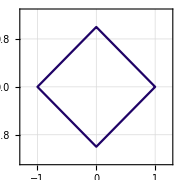

-Graphics-

-Graphics3D-

-Graphics3D-

-Graphics3D-

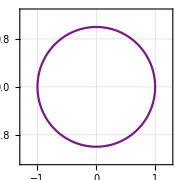

```mathematica
l2 = ContourPlot[Sqrt[(Abs[x]^2+Abs[y]^2)] ==1, {x,-1.25,1.25},{y,-1.25,1.25}, ImageSize->Small, GridLines->Automatic, ColorFunction->"Rainbow"]
```

l2Norm.png

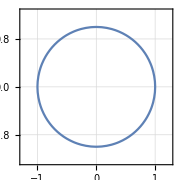

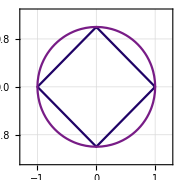

NormBalls.png

```mathematica
Export["l2Norm.png", ContourPlot[(Abs[x]^2+Abs[y]^2)^(1/2) ==1, {x,-1.25,1.25},{y,-1.25,1.25}, ImageSize->Small, GridLines->Automatic]]

ContourPlot[Sqrt[(Abs[x]^2+Abs[y]^2)] ==1, {x,-1.25,1.25},{y,-1.25,1.25}, ImageSize->Small, GridLines->Automatic]

Show[l1,l2]
Export["NormBalls.png",Show[l1,l2]]
```

```mathematica
SetOptions[$FrontEnd,Magnification->2.25]
```

```mathematica
l13d = ContourPlot3D[(Abs[x]^1+Abs[y]^1 + Abs[z]^1)== 1, {x, -1.0, 1.0},{y, -1.0,1.0},{z, -1.0,1.0},ImageSize->Small]
```

-Graphics3D-